## Differences between primes

```mathematica
(*results={};*)
n=10;primes=allPrimes[[n,;;10000]];
```

## Prime 10

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
(* Removed first, 2 -> 3, the only transition with d = 1 *)
```

## Visibility Graph

```mathematica
visibles={};Do[
Do[
If[visibleQ[i,j,diffs],AppendTo[visibles,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
igv10=Graph[visibles, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv10];
```

```mathematica
count = Total[adj]//Counts
```

<|2→1325,5→1247,3→1985,7→598,13→154,19→42,4→1619,9→359,8→469,11→213,6→844,17→62,18→54,25→14,15→106,10→246,14→127,31→13,12→174,23→21,22→28,24→17,61→1,26→19,16→76,37→5,21→32,43→2,46→4,48→4,73→1,28→15,33→12,29→5,20→41,27→10,30→8,39→5,38→5,36→7,35→3,34→4,32→4,40→3,45→1,53→2,60→2,74→1,65→1,87→1,42→3,47→1,57→1,44→1,54→1,1→1|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{2,1325/9999},{5,1247/9999},{3,1985/9999},{7,598/9999},{13,14/909},{19,14/3333},{4,1619/9999},{9,359/9999},{8,469/9999},{11,71/3333},{6,844/9999},{17,62/9999},{18,6/1111},{25,14/9999},{15,106/9999},{10,82/3333},{14,127/9999},{31,13/9999},{12,58/3333},{23,7/3333},{22,28/9999},{24,17/9999},{61,1/9999},{26,19/9999},{16,76/9999},{37,5/9999},{21,32/9999},{43,2/9999},{46,4/9999},{48,4/9999},{73,1/9999},{28,5/3333},{33,4/3333},{29,5/9999},{20,41/9999},{27,10/9999},{30,8/9999},{39,5/9999},{38,5/9999},{36,7/9999},{35,1/3333},{34,4/9999},{32,4/9999},{40,1/3333},{45,1/9999},{53,2/9999},{60,2/9999},{74,1/9999},{65,1/9999},{87,1/9999},{42,1/3333},{47,1/9999},{57,1/9999},{44,1/9999},{54,1/9999},{1,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.124432/x^0.609574]

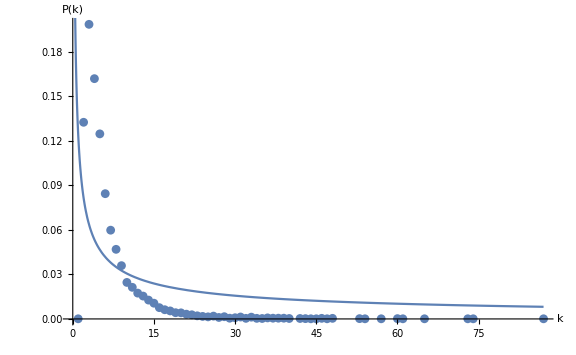

```mathematica
vis10=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-10.eps",vis10];
```

## Mean degree

```mathematica
degree=VertexDegree[igv10]//Mean//N;
```

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

AppendTo::rvalue: results is not a variable with a value, so its value cannot be changed.

## Horizontal Visibility Graph

```mathematica
horizontals={};Do[
Do[
If[horizontalQ[i,j,diffs],AppendTo[horizontals,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
igh10=Graph[horizontals, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh10];
```

```mathematica
count = Total[adj]//Counts
```

<|1→2,2→3493,4→1490,3→2298,5→957,6→607,7→404,8→259,9→170,11→77,12→38,13→21,14→17,15→18,17→4,10→127,16→9,20→4,18→3,19→1|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[2;;]]
```

{{2,3493/9999},{4,1490/9999},{3,766/3333},{5,29/303},{6,607/9999},{7,4/99},{8,259/9999},{9,170/9999},{11,7/909},{12,38/9999},{13,7/3333},{14,17/9999},{15,2/1111},{17,4/9999},{10,127/9999},{16,1/1111},{20,4/9999},{18,1/3333},{19,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x];
```

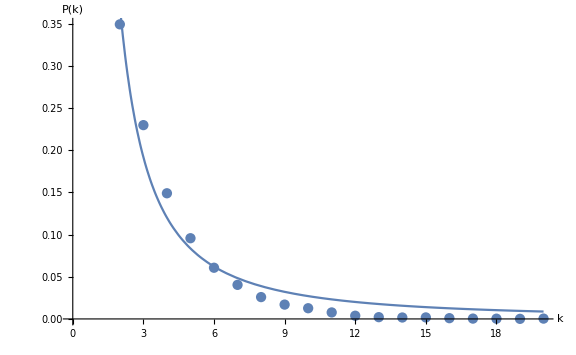

```mathematica
hvis10=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-10.eps",hvis10];
```

## Mean degree

```mathematica
degree=VertexDegree[igh10]//Mean//N;
```

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

AppendTo::rvalue: results is not a variable with a value, so its value cannot be changed.

## Return result

```mathematica
results
```

results